```mathematica
DataStatistic[x_List]:=Module[{mean,tValue=1.14,deltaB=0.0004,uncertainty},MeanStandardDeviation[data_]:=StandardDeviation[data]/Sqrt[Length[data]];
DeltaA[data_,t_]:=t*StandardDeviation[data];
Uncertainty[data_,t_,deltaB_]:=Sqrt[DeltaA[data,t]^2+deltaB^2];mean=Mean[x];
uncertainty=Uncertainty[x,tValue,deltaB];
Print["Mean: ",mean];
Print["Standard Deviation: ",StandardDeviation[x]];
Print["Mean Standard Deviation: ",MeanStandardDeviation[x]];
Print["deltaA: ",DeltaA[x,tValue]];
Print["deltaB: ",deltaB];
Print["Uncertainty: ",uncertainty];
Return[Around[mean,uncertainty]]];

ShowFitPlot[dataX_List,dataY_List,xName_,yName_,plotName_]:=Module[{data,fitModel},data=Transpose[{dataX,dataY}];
fitModel=LinearModelFit[data,x,x];
Print["Best Fit Equation: ",fitModel["BestFit"]];
Print[Show[ListPlot[data,PlotStyle->Red,PlotLabel->plotName,AxesLabel->{xName,yName}],Plot[fitModel[x],{x,Min[dataX],Max[dataX]}]]];
Return[fitModel["BestFitParameters"]]];
ShowFitPlot[dataX_List,dataY_List,xName_,yName_]:=ShowFitPlot[dataX,dataY,xName,yName,""];
ShowFitPlot[dataX_List,dataY_List]:=ShowFitPlot[dataX,dataY,"","",""];
```

```mathematica
dData={0,2,3,5,3,0}*0.0001+0.0640
```

{0.064,0.0642,0.0643,0.0645,0.0643,0.064}

```mathematica
DD=2.858
```

2.858

```mathematica
L=72.25
```

72.25

```mathematica
H=69.80
```

69.8

```mathematica
d=DataStatistic[dData]
```

Mean: 0.0642167

Standard Deviation: 0.000194079

Mean Standard Deviation: 0.0000792324

deltaA: 0.00022125

deltaB: 0.0004

Uncertainty: 0.000457112

0.06420.0005

```mathematica
mdata=Table[i,{i,1,11}]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
xdata1={0.1,0.83,1.42,2.07,2.44,2.84,3.21,3.92,4.60,5.21,5.71}
```

{0.1,0.83,1.42,2.07,2.44,2.84,3.21,3.92,4.6,5.21,5.71}

Best Fit Equation: 0.60194+1.83551 x

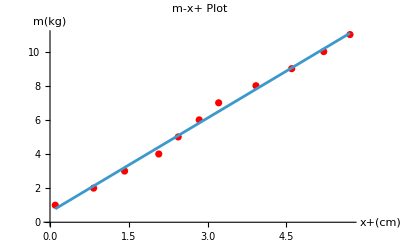

1.83551

```mathematica
k1=ShowFitPlot[xdata1,mdata,"x+(cm)","m(kg)","m-x+ Plot"][[2]]
```

```mathematica
xdata2={0.12,0.80,1.38,1.95,2.42,2.79,3.28,3.94,4.60,5.20,5.73}
```

{0.12,0.8,1.38,1.95,2.42,2.79,3.28,3.94,4.6,5.2,5.73}

Best Fit Equation: 0.662717+1.82273 x

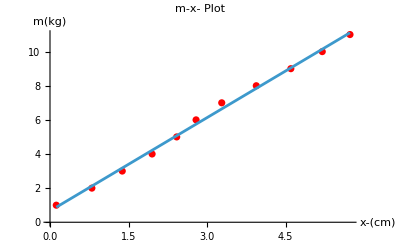

1.82273

```mathematica
k2=ShowFitPlot[xdata2,mdata,"x-(cm)","m(kg)","m-x- Plot"][[2]]
```

```mathematica
k=Mean[{k1,k2}]
```

1.82912

```mathematica
g=9.794
```

9.794

```mathematica
EE=(8g L H)/(Pi d^2 DD)k*10^4
```

1.9520.02810^11